## Geometric mean between r_1 and r_3 of three tangent circles

### Illustrating the relationship among the Geometric Mean, Arithmetic Mean and the Harmonic Mean

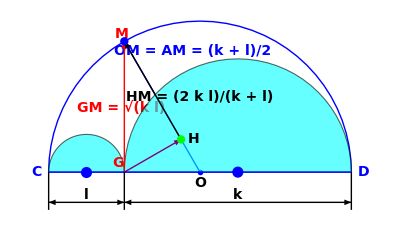

```mathematica
cir[{x_,y_},rad_,angle_]={Thick,Blue,Circle[{x,y},r,{0,π}],PointSize[0.01],Point[{x,y}]};
r=1;
y[x_]:= Sqrt[(r^2 -(x-r)^2)];
Graphics[{
cir[{r,0},1,{0,π}],{Thick,Blue,Arrow[{{r,0},{0.5 r,y[0.5 r]}}],
{EdgeForm[{Thick,Black}],FaceForm[Cyan],Opacity[0.6],Disk[{0.25 r,0},0.25 r,{0,π}],Disk[{1.25 r,0},0.75 r,{0,π}]},PointSize[0.02],Blue,Point[{0.25 r,0}],Point[{1.25 r,0}],
Red,Arrow[{{0.5r,0},{0.5 r,y[0.5 r]}}],(*{Red,Dashing[0.03],Circle[{0.5 r,0},y[0.5 r],{0,π}]},*)Purple,Arrow[{{.5r,0},{3.5 r/4,√3 r/8}}],Black,Arrow[{{3.5 r/4,√3 r/8},{.5 r,y[.5 r]}}],
PointSize[0.015],Green,Point[{3.5 r/4,√3 r/8}],Blue,Point[{0.5 r,y[0.5 r]}],
Line[{{0,0},{2r,0}}]},
Inset[Style["C ",14,Bold,Blue],{-0.08,0}],Inset[Style["G ",14,Bold,Red],{0.46 r,0.06}],
Inset[Style["D ",14,Bold,Blue],{2. r+0.08,0}],Inset[Style["M ",14,Bold,Red],{0.48 r,y[0.48 r]+0.06}],
Inset[Style["GM = √(k l) ",14,Bold,Red],{0.48 r,y[0.48 r]/2}],
Inset[Style[" HM = (2 k l)/(k + l) ",14,Bold,Black,Italic],{ r,r/2}],
Inset[Style["OM = AM = (k + l)/2 ",14,Bold,Blue,Italic],{ 0.95r,0.8r}],
Inset[Style["H ",14,Bold,Black],{3.5 r/4+0.08,√3 r/8}],
Inset[Style["O ",14,Bold],{ r,-0.07}],Black,
Inset[Style["k ",14,Bold,Italic],{ 5r/4,-0.15}],Black,
Inset[Style["l ",14,Bold,Italic],{ r/4,-0.15}],Black,
Line[{{0,0},{0,-0.25}}],Line[{{0.5 r,0},{.5 r, -0.25}}],Line[{{2r,0},{2 r,-0.25}}],
Arrowheads[{-0.03,0.03}],Arrow[{{0,-0.2},{0.5 r,-0.2}}],Arrow[{{0.5r,-0.2},{2 r,-0.2}}]



},AxesOrigin->{0,0},Axes->False]
```

### Simple Example

```mathematica
Module[{r1,r3,u,v,m1,m2,answer,check},Manipulate[
cir[center_,radius_]={Thick,Circle[center,radius],PointSize[0.01],Point[{center}]};
dsc[center_,radius_]={Disk[center,radius],PointSize[0.01],Point[{center}]};
r2:=√(r1 r3);alpha:=ArcSin[(r3-r2)/(r3+r2)];

m1:=r1 Cot[alpha]+r1 Cos[alpha]/2;m2:=r2 Cot[alpha]+r2 Cos[alpha]-r1 Cos[alpha]/2;

If[u<m1,u=m1];If[u>m2,u=m2];(*alpha=ArcSin[(r3-r1)/(r1+2 r2 +r3)];*)

If[v<r2 Cot[alpha],v=Dynamic[r2 Cot[alpha]]];
If[v>r3( Cot[alpha]-Cos[alpha]),v=r3( Cot[alpha]-Cos[alpha])];

Column[{
Item[
If[answer,Style[Row[{"\nradius of the middle circle = ",r2,"\nThe geometric mean between r1 = ",r1," and r3 = ",r3," is ",r2,"\n"}],14,Italic,Purple],Style[Row[{"\nGiven three tangent circles as shown with\n smallest radius r1 = ",r1," and largest radius r3 = ",r3, "\nCalculate the radius of the middle circle as well\n as the geometric mean between r1 and r3\n"}],12, Black]
],Alignment->Left,Frame->True],
Item[
grthree=Graphics[{cir[{r1 Cot[alpha],r1},r1],Purple,cir[{r2 Cot[alpha],r2},r2],Black,cir[{r3 Cot[alpha],r3},r3],
PointSize[0.01],Point[{r3 (Cot[alpha]-Cos[alpha]),r3(1- Sin[alpha])}],

(*{EdgeForm[{Thick,Black}],FaceForm[Cyan],Disk[{u,u Tan[alpha]},r1,{alpha,π+alpha}],PointSize[0.015],Point[{u,u Tan[alpha]}]},*)

If[answer,{{EdgeForm[{Thick,Black}],FaceForm[Cyan],(*Disk[{u,u Tan[alpha]},r1,{alpha,π+alpha}],PointSize[0.015],Point[{u,u Tan[alpha]}]},*)
Disk[{r1 Cot[alpha]+r1 Cos[alpha]/2,r1+r1 Tan[alpha]/2},r1/2,{alpha,π+alpha}],PointSize[0.015],Point[{r1 Cot[alpha]+r1 Cos[alpha]/2,r1+r1 Tan[alpha]/2}]},

{EdgeForm[{Thick,Purple}],FaceForm[Yellow],Opacity[0.4],Disk[{r2 Cot[alpha],r2},r2,{alpha,π+alpha}],PointSize[0.01],Point[{r2 Cot[alpha],r2}]},

EdgeForm[{Thick,Black}],FaceForm[Cyan],Opacity[0.6],Disk[{r3 Cot[alpha]-r3/2 Cos[alpha],r3-(r3/2)Sin[alpha]},r3/2,{alpha,π+alpha}],PointSize[0.007],Point[{r3 Cot[alpha]-r3/2 Cos[alpha],r3-(r3/2)Sin[alpha]}],{Thick,Blue,Circle[{(r3 Cot[alpha] +r3 (Cot[alpha]-Cos[alpha])-r1 Cos[alpha])/2 ,((r3 Cot[alpha] +r3 (Cot[alpha]-Cos[alpha])-r1 Cos[alpha])/2) Tan[alpha]},(r3 +r1)/2,{alpha,π+alpha}]},Red,PointSize[0.01],Point[{(r3 Cot[alpha] +r3 (Cot[alpha]-Cos[alpha])-r1 Cos[alpha])/2 ,((r3 Cot[alpha] +r3 (Cot[alpha]-Cos[alpha])-r1 Cos[alpha])/2) Tan[alpha]}],
Arrow[{{r3 (Cot[alpha]-Cos[alpha]),r3(1- Sin[alpha])},{r3 (Cot[alpha]-Cos[alpha])-r2 Sin[alpha],r3(1- Sin[alpha])+r2 Cos[alpha]}}],Inset[Style[Row[{Style[" r = GM (r1, r3)\n ",12,Black]," = ",r2}],12],{r3 (Cot[alpha]-Cos[alpha])-r2 Sin[alpha]+3,(r3(1- Sin[alpha])+r2 Cos[alpha])0.9}]},{}],
If[check,{{EdgeForm[{Thick,Black}],FaceForm[Cyan],Disk[{u,u Tan[alpha]},r1/2,{alpha,π+alpha}],PointSize[0.015],Point[{u,u Tan[alpha]}]},{EdgeForm[{Thick,Purple}],FaceForm[Yellow],Opacity[0.4],Disk[{v,v Tan[alpha]},r2,{alpha,π+alpha}],PointSize[0.01],Point[{v,v Tan[alpha]}]}},{}],
Line[{{r1 Cot[alpha],r1},{r1 Cot[alpha],0}}],Line[{{r2 Cot[alpha],r2},{r2 Cot[alpha],0}}],Line[{{r3 Cot[alpha],r3},{r3 Cot[alpha],0}}],
Text[Style[Row[{"r1 = ",r1}],Small],{r1 Cot[alpha],r1/2}],
Text[Style[Row[{"r3 = ",r3}],Small],{r3 Cot[alpha],r3/2}],
If[answer,Text[Style[Row[{"r2 = ",r2}],Small],{r2 Cot[alpha],3r2/2}],
Text[Style["r2 = ?",Small],{r2 Cot[alpha],r2/2}]]


},Axes->True,AxesLabel->{Style["x",Large,Bold,Italic],Style["y",Large,Bold,Italic]},
AxesStyle->{{Arrowheads[{-0.04,0.04}],Directive[Thick,Italic,Black,14]},{Arrowheads[{-0.04,0.04}],Directive[Thick,Italic,Black,14]}},AxesOrigin->{0,0}];

plotcntrLine=Plot[{ x Tan[alpha]},{x,-3,1.5r3 Cot[alpha] },PlotStyle->{Red,Dashing[{0.001,0.02,0.14,0.02}]}];
plotTangtLine=Plot[{ x Tan[2 alpha]},{x,-3,r3 Cot[alpha] },PlotStyle->{Blue}];
Show[grthree,plotcntrLine,plotTangtLine,ImageSize->400],Alignment->{Center},Frame->True]
}],
Grid[{
{Control[{{r1 ,2.,"radius1"},2.,5,Appearance->"Labeled",ImageSize->Tiny}],Control[{{r3 ,9.,"radius3"},6.,15.,Appearance->"Labeled",ImageSize->Tiny}],Control[{{answer,False,"Answer"},{False,True}}]},{Control[{{u,m1,"cntr1"},m1,m2 (*r3 (Cot[alpha]-Cos[alpha])-r1 Cos[alpha]*),Appearance->"Labeled",ImageSize->Tiny,Enabled->check}],
Control[{{v,N[r2 Cot[alpha]],"cntr2"},Dynamic[r2 Cot[alpha]],r3( Cot[alpha]-Cos[alpha]),Appearance->"Labeled",ImageSize->Tiny,Enabled->check}],Control[{{check,False,"Check"},{False,True},Enabled->answer}]}
}],TrackedSymbols:>{r1,r3,m1,m2,answer,u,v,check}]]
```

### Two-step Example

Given five tangent circles and the radius of the smallest and the largest one.  Find the radius of the middle one.

```mathematica
Module[{r1,r5,answer},Manipulate[
r3=√(r1 r5);r2=√(r1 r3);r4=√(r3 r5);

alpha:=ArcSin[(r5-r4)/(r4+r5)];
cir[center_,radius_]={Thick,Circle[center,radius],PointSize[0.015],Point[{center}]};

Column[{
Item[If[answer,Style[Row[{"\nThe radius of the third circle = ",r3, " cm\n"}],16,Purple],Style[Row[{"\nThe smallest circle of the five tangent circles\n has radius = ",r1," cm and the largest has radius = ", r5, " cm\n Find the radius of the middle circle\n"}],16,Black]],Alignment->Left,Frame->True],
Item[
gcircle=Graphics[{cir[{0,r1},r1],Blue,cir[{(r1+r2)Cos[alpha],r2},r2],Purple,cir[{(r1+2r2+r3)Cos[alpha],r3},r3],Red,cir[{(r1+2r2+2r3+r4)Cos[alpha],r4},r4],Black,
cir[{(r1+2r2+2r3+2 r4+r5)Cos[alpha],r5},r5],Line[{{0,r1},{0,0}}],Line[{{(r1+2r2+2r3+2 r4+r5)Cos[alpha],r5},{(r1+2r2+2r3+2 r4+r5)Cos[alpha],0}}],Purple,Line[{{(r1+2r2+r3)Cos[alpha],r3},{(r1+2r2+r3)Cos[alpha],0}}],

Text[Style[Row[{"r1 = ",r1, " cm"}],12,Black],{0,r1/2}],
If[answer,Text[Style[Row[{"r3 = ",r3, " cm"}],12,Purple],{(r1+2r2+r3)Cos[alpha],r3/2}],Text[Style[Row[{"r = ? cm"}],12,Purple],{(r1+2r2+r3)Cos[alpha],r3/2}]],
Text[Style[Row[{"r5 = ",r5, " cm"}],12,Black],{(r1+2r2+2r3+2 r4+r5)Cos[alpha],r5/2}]
},Axes->False,PlotRange->{{-20,220},{-20,90}}];
pline=Plot[{0,x Tan[2 alpha]+2 r1},{x,-20,210},PlotRange->All,PlotStyle->Purple];
Show[gcircle,pline,ImageSize->Large],Alignment->{Center},Frame->True,ItemSize->{40,10}]
}],
Row[{Control[{{r1 ,12,"radius1"},7,18,Appearance->"Labeled",ImageSize->Tiny}],Spacer[15],Control[{{r5 ,18,"radius5"},18.,30.,Appearance->"Labeled",ImageSize->Tiny}],Spacer[15],Control[{{answer,False,"Answer"},{False,True}}]
}],TrackedSymbols:>{r1,r5,answer}]]
```

### General Case (n odd)

We notice that r_3 is the radius of the middle circle between the smallest and the largest;
r_3 was also the middle circle between r_2 and r_2;  r_4 is the middle circle between the third and fifth circles.
Therefore, the general case for the odd number of circles is :   r_((n+1)/2)= √(r1 r_n)
where r_n  is the radius of the n-circle.

In general, for odd number of tangent circles, from the above observation and from the previous example:  r_((k + j)/2) = √(r_k r_j)
where r_k  and r_j  are the radii of the k^th and j^th circles, and both j and k are either odd or even numbers.

Taking the above equations one step further, we find the general formula for the radius in this scheme to be:

r(k)=r_1^((n-k)/(n-1))r_n^((k-1)/(n-1))

and

sin(α)==(r_n^(1/(n-1))-r_1^(1/(n-1)))/(r_n^(1/(n-1))+r_n^(1/(n-1)))

### Demonstration of General Case

Given n tangent circles and the radius of the smallest and the largest one.  Find the general formula of the radius

```mathematica
Module[{r1,rn,answer,n},Manipulate[

r[k_]:=r1^((n-k)/(n-1)) ( rn^((k-1)/(n-1)));
alpha=ArcSin[(rn^(1/(n-1))- r1^(1/(n-1)))/(rn^(1/(n-1))+ r1^(1/(n-1)))];

cir[center_,radius_]={Thick,Circle[center,radius],PointSize[0.015],Point[center]};

Column[{
Item[Which[
answer&&OddQ[n],Row[{Style["\nThe explicit formula for kth radius in terms of the first and the last circle is\n\nr[k] = r1^((n-k)/(n-1)) rn^((k-1)/(n-1))\n",18,Black],
Style[Row[{"\nThe radius of the middle circle = ",r[(n+1)/2], " cm\n"}],16,Purple]}],answer&&EvenQ[n],Row[{Style["\nThe explicit formula for kth radius in terms of the first and the last circle is\n\nr[k] = r1^((n-k)/(n-1)) rn^((k-1)/(n-1))\n",18,Black],Style[Row[{"\nThe radius of the middle plus one circle = ",r[(n)/2+1], " cm\n"}],16,Purple]}], True,
Style[Row[{"\nThe smallest circle of the five tangent circles\n has radius = ",r[1]," cm and the largest has radius = ", rn, " cm\n Find the explicit formula for the radius, and the radius of the middle circle if # circles is odd\n"}],16,Black]],Alignment->Left,Frame->True],
Item[
gcircle=Graphics[{Black,
Table[cir[{r[i]Cot[alpha],r[i]},r[i]],{i,1,n}],
(*cir[{r[n] Cot[alpha],r[n]},r[n]],*)Line[{{r1 Cot[alpha],r1},{r1 Cot[alpha],0}}],Line[{{r[n]Cot[alpha],r[n]},{(r[n])Cot[alpha],0}}],Purple,If[OddQ[n],Line[{{(r[(n+1)/2])Cot[alpha],r[(n+1)/2]},{(r[(n+1)/2])Cot[alpha],0}}],Line[{{(r[(n)/2+1])Cot[alpha],r[(n)/2+1]},{(r[(n)/2+1])Cot[alpha],0}}]],

Text[Style[Row[{"r1 = ",r[1], " cm"}],12,Black],{r[1] Cot[alpha],r[1]/2}],
Which[answer&&OddQ[n],Text[Style[Row[{Subscript[r,(n+1)/2]," = ",r[(n+1)/2], " cm"}],12,Purple],{r[(n+1)/2] Cot[alpha],((n+1)/2)r[(n+1)/2]/2}],OddQ[n],Text[Style[Row[{"r = ? cm"}],12,Purple],{r[(n+1)/2] Cot[alpha],r[(n+1)/2]/2}],answer&&EvenQ[n],Text[Style[Row[{Subscript[r,(n)/2+1]," = ",r[(n)/2+1], " cm"}],12,Purple],{r[(n)/2+1] Cot[alpha],((n)/2+1)r[(n)/2+1]/2}],EvenQ[n],Text[Style[Row[{"r = ? cm"}],12,Purple],{r[(n)/2+1] Cot[alpha],r[(n)/2+1]/2}]],
Text[Style[Row[{Subscript[r,n]," = ",r[n], " cm"}],12,Black],{r[n] Cot[alpha],r[n]/2}]
},Axes->False,PlotRange->Automatic];
plotcntrLine=Plot[{0, x Tan[alpha]},{x,0.93 r[1]1  Cot[alpha],1.03r[n ]Cot[alpha] },PlotStyle->{{Thick,Purple},{Red,Dashing[{0.001,0.02,0.14,0.02}]}}];
plotTangtLine=Plot[{ x Tan[2 alpha]},{x,0.93 r[1]  Cot[alpha],1.03r[n ]Cot[alpha] },PlotStyle->{Blue}];
Show[gcircle,plotcntrLine,plotTangtLine,ImageSize->Large,PlotRange->All],Alignment->{Center},Frame->True,ItemSize->{40,10}]
}],
Row[{
Control[{{n ,5,"No.\n Tan. Circ"},3,25,1,Appearance->"Labeled",ImageSize->Tiny}],Spacer[10],
Control[{{r1 ,12,"radius1"},1,13,Appearance->"Labeled",ImageSize->Tiny}],Spacer[15],Control[{{rn,48,"radius5"},11,100.,Appearance->"Labeled",ImageSize->Tiny}],Spacer[15],Control[{{answer,False,"Answer"},{False,True}}]
}],TrackedSymbols:>{n,r1,rn,answer}]]
```